```mathematica
Clear["Global`*"]
```

```mathematica
Get["TSPnew3"];
```

### 基本閉路行列の関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
Pin={{0,0},{1,2},{1.5,0.5},{3,0.7},{3.5,3.3},{5,0}}(*Point input*)
```

{{0,0},{1,2},{1.5,0.5},{3,0.7},{3.5,3.3},{5,0}}

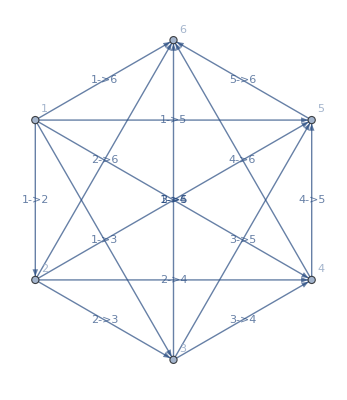

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"](*Ggraph input*)
```

```mathematica
h=LoopMatrix[Gin]
```

{{0,0,0,1,-1,0,0,0,0,0,0,0,0,0,1},{0,0,1,0,-1,0,0,0,0,0,0,0,0,1,0},{0,0,1,-1,0,0,0,0,0,0,0,0,1,0,0},{0,1,0,0,-1,0,0,0,0,0,0,1,0,0,0},{0,1,0,-1,0,0,0,0,0,0,1,0,0,0,0},{0,1,-1,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,0,0,-1,0,0,0,1,0,0,0,0,0,0},{1,0,0,-1,0,0,0,1,0,0,0,0,0,0,0},{1,0,-1,0,0,0,1,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0,0,0}}

```mathematica
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}](* Point Distance *)
```

{√5,1.58114,3.08058,4.81041,5,1.58114,2.38537,2.8178,2 √5,1.51327,3.44093,3.53553,2.64764,2.11896,3.62491}

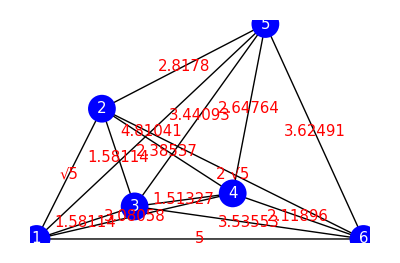

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gin]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[PD[[i]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}]
```

```mathematica
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD
```

{{√5,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.,1.58114,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,3.08058,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,4.81041,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0},{0.,0.,0.,0.,0.,1.58114,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,2.38537,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,2.8178,0.,0.,0.,0.,0.,0.,0.},{0,0,0,0,0,0,0,0,2 √5,0,0,0,0,0,0},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.51327,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.44093,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.53553,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.64764,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.11896,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.62491}}

```mathematica
s=Table[0,{i,Length[EdgeRules[Gin]]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Point *)
```

{{{5,0},{0,0},{3.5,3.3}},{{5,0},{0,0},{3,0.7}},{{3.5,3.3},{0,0},{3,0.7}},{{5,0},{0,0},{1.5,0.5}},{{3.5,3.3},{0,0},{1.5,0.5}},{{3,0.7},{0,0},{1.5,0.5}},{{5,0},{0,0},{1,2}},{{3.5,3.3},{0,0},{1,2}},{{3,0.7},{0,0},{1,2}},{{1.5,0.5},{0,0},{1,2}}}

```mathematica
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}](* 右回りならば負、左回りならば正 *)
```

{-1,-1,1,-1,1,-1,-1,-1,-1,-1}

```mathematica
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}](* Fundamental Loop Area *)
```

{8.25,1.75,3.725,1.25,1.6,0.225,5,1.85,2.65,1.25}

```mathematica
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}](* 誘導起電力は右回りなら負、左回りなら正 *)
```

{-8.25,-1.75,3.725,-1.25,1.6,-0.225,-5,-1.85,-2.65,-1.25}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)(* 誘導起電力行列を考慮した電流を求める式 *)
```

{-0.671869,0.176089,0.298125,-0.385242,0.582897,0.335685,-0.0961094,-0.781044,-0.130401,0.274226,-0.15449,0.392038,0.360106,0.116135,-0.96067}

```mathematica
Reverse[Ordering[Abs[Curr]]]
```

{15,8,1,5,12,4,13,6,3,10,2,11,9,14,7}

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

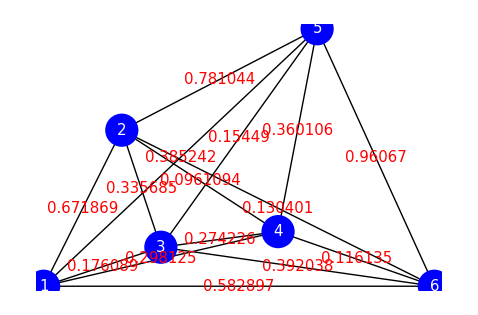

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[StyleForm[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[StyleForm[Abs[Curr[[i]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
MaxPartLoop={};
For[j=3,Length[MaxPartLoop]==0,j++,
MaxPartLoop=FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[Range[j]]]]]],
Infinity,All];
j++;
]
MaxPartLoop=EdgeRules[MaxPartLoop[[1]]]
```

{6→5,5→2,2→1,1→6}

```mathematica
RestVertex=Delete[VertexList[Gin],Table[{VertexList[MaxPartLoop][[i]]},{i,Length[VertexList[MaxPartLoop]]}]]
```

{3,4}

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiff[MaxPartLoop[[1]],RestVertex[[1]]]
```

3.35155

```mathematica
MinTriTourDiff=Min[Table[TriTourDiff[MaxPartLoop[[i]],RestVertex[[1]]],{i,Length[MaxPartLoop]}]]
```

0.116673

```mathematica
VertexList[{DelEdge}]
```

{1,6}

```mathematica
InsertPartLoop=Append[Append[Delete[MaxPartLoop,MinTriTourDiffPosition],VertexList[{DelEdge}][[1]]->RestVertex[[1]]],RestVertex[[1]]->VertexList[{DelEdge}][[2]]]
```

{6→5,5→2,2→1,1→3,3→6}

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
TriTourDiffList[InsertPartLoop,RestVertex[[2]]]
```

{1.14169,2.21521,3.22989,3.01272,0.0967027}

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinTriTourDiffPosition[InsertPartLoop,RestVertex[[2]]]
```

5

```mathematica
DelEdge[PartLoop_,Vertex_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,Vertex]]]
```

```mathematica
DelEdge[InsertPartLoop,RestVertex[[2]]]
```

3→6

```mathematica
VertexInsertPartLoop[PartLoop_,Vertex_]:=(
Append[Append[Delete[PartLoop,MinTriTourDiffPosition[PartLoop,Vertex]],VertexList[{DelEdge[PartLoop,Vertex]}][[1]]->Vertex],Vertex->VertexList[{DelEdge[PartLoop,Vertex]}][[2]]]
)
```

```mathematica
VertexInsertPartLoop[InsertPartLoop,RestVertex[[2]]]
```

{6→5,5→2,2→1,1→3,3→4,4→6}